```mathematica
ClearAll["Global`*"]
```

```mathematica
dir=NotebookDirectory[];
SetDirectory@dir;
```

## Getting Nodes for Interpolant from Dopplet Ultrasound Plot

http://reference.wolfram.com/language/howto/GetCoordinatesForPointsInAPlot.html

```mathematica
Import@"doppler.jpg"
```

-Graphics-

```mathematica
nodes={{219.3,115.6},{174.3,101.2},{213.3,87.10000000000001},{230.09999999999997,131.5},{145.5,131.5}};
```

```mathematica
f1=BezierFunction[nodes]
f2=Interpolation[nodes,InterpolationOrder->1]
```

BezierFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{145.5, 230.1}}, <>]

InterpolatingFunction::dmval: Input value {139.68} lies outside the range of data in the interpolating function. Extrapolation will be used.

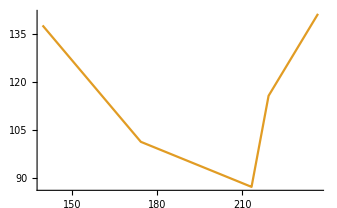

```mathematica
Plot[{f1[x],f2[x]},{x,139.67821782178217,236.71782178217822}]
```

```mathematica
f2=FindFormula[nodes,x,PerformanceGoal->"Quality", SpecificityGoal->Infinity]
```

933390.-38609.3 x+677.673 x^2-6.54554 x^3+0.0375942 x^4+2.41868×10^-7 x^6-1.93659×10^-10 x^7-0.000128455 Abs[x]^5-1.67691 Cos[Abs[x]]+0.0375942 Cot[x]-2.12869 Sin[x]+3.13604 Sin[0.115655-x-Sin[x]]^4

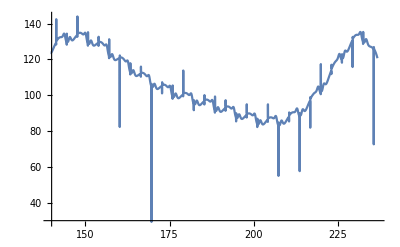

```mathematica
Plot[f2,{x,139.67821782178217,236.71782178217822},PlotRange->All]
```

```mathematica
Subscript[Δ, CS]=35/40;
Subscript[Δ, d]=6/7 Subscript[Δ, CS];
Subscript[t, 0]=2(Subscript[Δ, CS]-Subscript[Δ, d]);
```

```mathematica
int1=Interpolation@{{{0},0,0},{{Subscript[t, 0]},1.5,0}};
```

```mathematica
int2=Interpolation@{{{0},1.5,0},{{Subscript[Δ, d]},.7,0},{{Subscript[Δ, CS]},1.5,0}};
```

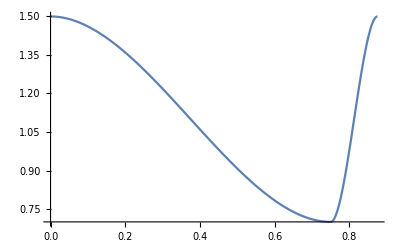

```mathematica
Plot[int2[x],{x,0,Subscript[Δ, CS]}]
```

```mathematica
A[x_]:=Piecewise[{{int1@x, x<Subscript[t, 0]}, {int2@Mod[x-Subscript[t, 0],Subscript[Δ, CS]], True}}]
```

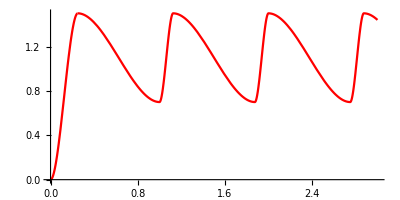

```mathematica
Plot[A[x],{x,0,3},
AspectRatio->Automatic,
AxesOrigin->{0,0},
PlotStyle->Red,
ImageSize->{400}
]
```